Fourier series for a sawtooth function

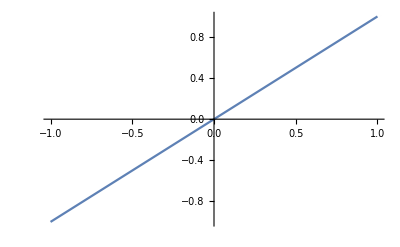

```mathematica
Plot[x,{x,-1,1}]
```

Since the sawtooth function is odd, expand in the set of odd basis functions sin(nπx/L), where L is half the period.

```mathematica
b[n_]=-(-1)^n*2*L/(n*Pi)
```

(2 (-1)^(1+n) L)/(n π)

Use the coefficients and the sine basis functions to write the expansion for the sawtooth function:

```mathematica
f[m_]:=Sum[b[n]*Sin[n*Pi*x/L],{n,1,m}]
```

Important things to notice:

(1) Here’s an example of when you would want to use delayed evaluation for a function.  Notice the function definition has “:=” instead of “=”.  This means the function remains unevaluated until you actually call it.  The reason that’s useful is that Mathematica doesn’t know that n is an integer, and so may spend a lot of time trying to come up with a closed form for the solution.  Try it without the := to see what happens.

(2) Notice that the variable “m” passed to the function f is the highest value of n in the sum.  Asking for f[3] gives you the sum up to the n=3 term.

Always try out a few terms to see if they behave as you would expect:

```mathematica
f[1]
f[3]
```

(2 L Sin[(π x)/L])/π

(2 L Sin[(π x)/L])/π-(L Sin[(2 π x)/L])/π+(2 L Sin[(3 π x)/L])/(3 π)

Make some plots of the first few terms.  Set L=1 for plotting purposes

```mathematica
L=1;
```

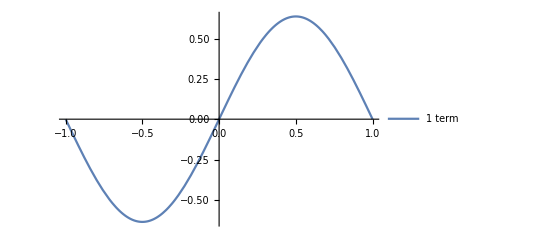
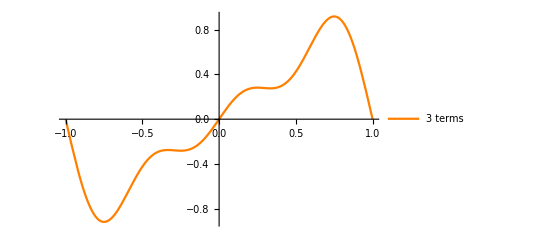
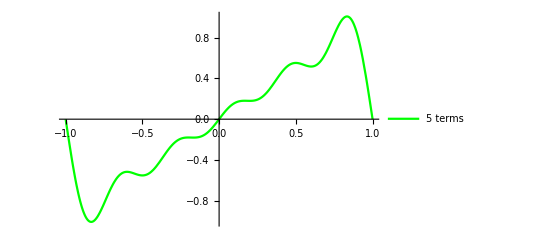

```mathematica
{Plot[f[1],{x,-1,1},PlotLegends->{"1 term"}],Plot[f[3],{x,-1,1},PlotLegends->{"3 terms"},PlotStyle->Orange],Plot[f[5],{x,-1,1},PlotLegends->{"5 terms"},PlotStyle->Green]}
```

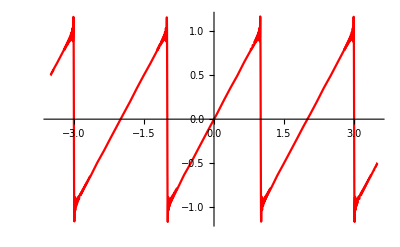

```mathematica
Plot[f[100],{x,-3.5,3.5},PlotStyle->Red]
```